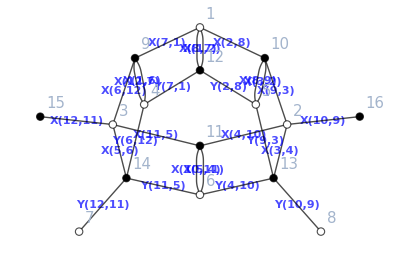

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=50;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
(*This is to fix my functional tests*)
```

```mathematica
(*This is to fix the getGrassmannian function*)
```

```mathematica
(*This is to fix the rotateExternalVertices function*)
```

```mathematica
(*input1={{1,{0.,0.}},{2,{6.,4.}},{3,{0.,5.}},{4,{0.4,-0.25}},{5,{6.,0.}},{6,{6.,-0.5}},{7,{1.114892969810759,0.}},{8,{0.,-0.75}},{9,{6.,-0.75}},{10,{0.,-0.5}}};
input2=Map[{input1[[#,2]],UndirectedEdge@@#}&,{{1,3},{1,7},{1,10},{2,5},{4,7},{5,6},{5,7},{6,9},{6,10},{8,10}}];
input3={2,3,4,8,9};*)
(*input1={{1,{0.,0.}},{2,{1.,6.}},{3,{0.,-1.}},{4,{1.,-2.}},{5,{0.,6.}},{6,{1.,0.}},{7,{1.,-1.}}};
input2=Map[{input1[[#,2]],UndirectedEdge@@#}&,{{1,3},{1,5},{1,6},{2,6},{3,7},{4,7},{6,7}}];
input3={2,4,5};*)
(*rotateExternalVertices[input1,input2,input3]*)
```